# SVM-BDT Comparison Results, 5/18/16

## Raw Data

## SVM: c, γ, Number of Support Vectors, False Positive Fraction, False Negative Fraction, Efficiency

```mathematica
SVMLinearHardRawData= Import [FileNameJoin[{NotebookDirectory[],"SVM","Results","linearhard0518"}], "Table"];
SVMLinearSoftRawData= Import [FileNameJoin[{NotebookDirectory[],"SVM","Results","linearsoft0518"}], "Table"];

SVMCircleHardRawData= Import [FileNameJoin[{NotebookDirectory[],"SVM","Results","circlehard0518"}], "Table"];
SVMCircleSoftRawData= Import [FileNameJoin[{NotebookDirectory[],"SVM","Results","circlesoft0518"}], "Table"];

SVMTwoCircleHardRawData= Import [FileNameJoin[{NotebookDirectory[],"SVM","Results","twocirclehard0518"}], "Table"];
SVMTwoCircleSoftRawData= Import [FileNameJoin[{NotebookDirectory[],"SVM","Results","twocirclesoft0518"}], "Table"];
```

## BDT: Number of Stumps, Efficiency, False Positive Fraction, False Negative Fraction

```mathematica
BDTLinearHardRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","Results","linearhard0518"}], "Table"];
BDTLinearSoftRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","Results","linearsoft0518"}], "Table"];

BDTCircleHardRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","Results","circlehard0518"}], "Table"];
BDTCircleSoftRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","Results","circlesoft0518"}], "Table"];

BDTTwoCircleHardRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","Results","twocirclehard0518"}], "Table"];
BDTTwoCircleSoftRawData= Import [FileNameJoin[{NotebookDirectory[],"BDT","Results","twocirclesoft0518"}], "Table"];
```

## Formatted Datasets

## SVM

### c-γ-Efficiency

```mathematica
SVMLinearHardCGE = SVMLinearHardRawData[[All,{1,2, 6}]];
SVMLinearSoftCGE = SVMLinearSoftRawData[[All,{1,2, 6}]];

SVMCircleHardCGE = SVMCircleHardRawData[[All,{1,2, 6}]];
SVMCircleSoftCGE = SVMCircleSoftRawData[[All,{1,2, 6}]];

SVMTwoCircleHardCGE = SVMTwoCircleHardRawData[[All,{1,2, 6}]];
SVMTwoCircleSoftCGE = SVMTwoCircleSoftRawData[[All,{1,2, 6}]];
```

### Log(c)-γ-Efficiency

```mathematica
SVMLinearHardLogCGE = MapAt[Log10, SVMLinearHardCGE, {All, 1}];
SVMLinearSoftLogCGE = MapAt[Log10, SVMLinearSoftCGE, {All, 1}];

SVMCircleHardLogCGE = MapAt[Log10, SVMCircleHardCGE, {All, 1}];
SVMCircleSoftLogCGE = MapAt[Log10, SVMCircleSoftCGE, {All, 1}];

SVMTwoCircleHardLogCGE = MapAt[Log10, SVMTwoCircleHardCGE, {All, 1}];
SVMTwoCircleSoftLogCGE = MapAt[Log10, SVMTwoCircleSoftCGE, {All, 1}];
```

### Efficiency-1 - False Positive Fraction

```mathematica
SVMLinearHardEFP= MapAt[1-#&,SVMLinearHardRawData[[All,{6,4}]],{All,2}];
SVMLinearSoftEFP= MapAt[1-#&,SVMLinearSoftRawData[[All,{6,4}]],{All,2}];

SVMCircleHardEFP = MapAt[1-#&,SVMCircleHardRawData[[All,{6,4}]],{All,2}];
SVMCircleSoftEFP = MapAt[1-#&,SVMCircleSoftRawData[[All,{6,4}]],{All,2}];

SVMTwoCircleHardEFP = MapAt[1-#&,SVMTwoCircleHardRawData[[All,{6,4}]],{All,2}];
SVMTwoCircleSoftEFP = MapAt[1-#&,SVMTwoCircleSoftRawData[[All,{6,4}]],{All,2}];
```

### Efficiency-1 - False Negative Fraction

```mathematica
SVMLinearHardEFN= MapAt[1-#&,SVMLinearHardRawData[[All,{6,5}]],{All,2}];
SVMLinearSoftEFN= MapAt[1-#&,SVMLinearSoftRawData[[All,{6,5}]],{All,2}];

SVMCircleHardEFN = MapAt[1-#&,SVMCircleHardRawData[[All,{6,5}]],{All,2}];
SVMCircleSoftEFN = MapAt[1-#&,SVMCircleSoftRawData[[All,{6,5}]],{All,2}];

SVMTwoCircleHardEFN = MapAt[1-#&,SVMTwoCircleHardRawData[[All,{6,5}]],{All,2}];
SVMTwoCircleSoftEFN = MapAt[1-#&,SVMTwoCircleSoftRawData[[All,{6,5}]],{All,2}];
```

### False Positive Fraction-1 - False Negative Fraction

```mathematica
SVMLinearHardFPFN= MapAt[1-#&,SVMLinearHardRawData[[All,{4,5}]],{All,2}];
SVMLinearSoftFPFN= MapAt[1-#&,SVMLinearSoftRawData[[All,{4,5}]],{All,2}];

SVMCircleHardFPFN = MapAt[1-#&,SVMCircleHardRawData[[All,{4,5}]],{All,2}];
SVMCircleSoftFPFN= MapAt[1-#&,SVMCircleSoftRawData[[All,{4,5}]],{All,2}];

SVMTwoCircleHardFPFN = MapAt[1-#&,SVMTwoCircleHardRawData[[All,{4,5}]],{All,2}];
SVMTwoCircleSoftFPFN= MapAt[1-#&,SVMTwoCircleSoftRawData[[All,{4,5}]],{All,2}];
```

## BDT

### Stumps-Efficiency

```mathematica
BDTLinearHardSE = BDTLinearHardRawData[[All,{1,2}]];
BDTLinearSoftSE = BDTLinearSoftRawData[[All,{1,2}]];

BDTCircleHardSE = BDTCircleHardRawData[[All,{1,2}]];
BDTCircleSoftSE = BDTCircleSoftRawData[[All,{1,2}]];

BDTTwoCircleHardSE = BDTTwoCircleHardRawData[[All,{1,2}]];
BDTTwoCircleSoftSE = BDTTwoCircleSoftRawData[[All,{1,2}]];
```

### Efficiency-1 - False Positive Fraction

```mathematica
BDTLinearHardEFP = MapAt[1-#&,BDTLinearHardRawData[[All,{2,3}]],{All,2}];
BDTLinearSoftEFP = MapAt[1-#&,BDTLinearSoftRawData[[All,{2,3}]],{All,2}];

BDTCircleHardEFP = MapAt[1-#&,BDTCircleHardRawData[[All,{2,3}]],{All,2}];
BDTCircleSoftEFP = MapAt[1-#&,BDTCircleSoftRawData[[All,{2,3}]],{All,2}];

BDTTwoCircleHardEFP = MapAt[1-#&,BDTTwoCircleHardRawData[[All,{2,3}]],{All,2}];
BDTTwoCircleSoftEFP = MapAt[1-#&,BDTTwoCircleSoftRawData[[All,{2,3}]],{All,2}];
```

### Efficiency-1 - False Negative Fraction

```mathematica
BDTLinearHardEFN = MapAt[1-#&,BDTLinearHardRawData[[All,{2,4}]],{All,2}];
BDTLinearSoftEFN = MapAt[1-#&,BDTLinearSoftRawData[[All,{2,4}]],{All,2}];

BDTCircleHardEFN = MapAt[1-#&,BDTCircleHardRawData[[All,{2,4}]],{All,2}];
BDTCircleSoftEFN = MapAt[1-#&,BDTCircleSoftRawData[[All,{2,4}]],{All,2}];

BDTTwoCircleHardEFN = MapAt[1-#&,BDTTwoCircleHardRawData[[All,{2,4}]],{All,2}];
BDTTwoCircleSoftEFN = MapAt[1-#&,BDTTwoCircleSoftRawData[[All,{2,4}]],{All,2}];
```

### False Positive Fraction-1 - False Negative Fraction

```mathematica
BDTLinearHardFPFN = MapAt[1-#&,BDTLinearHardRawData[[All,{3,4}]],{All,2}];
BDTLinearSoftFPFN = MapAt[1-#&,BDTLinearSoftRawData[[All,{3,4}]],{All,2}];

BDTCircleHardFPFN = MapAt[1-#&,BDTCircleHardRawData[[All,{3,4}]],{All,2}];
BDTCircleSoftFPFN = MapAt[1-#&,BDTCircleSoftRawData[[All,{3,4}]],{All,2}];

BDTTwoCircleHardFPFN = MapAt[1-#&,BDTTwoCircleHardRawData[[All,{3,4}]],{All,2}];
BDTTwoCircleSoftFPFN = MapAt[1-#&,BDTTwoCircleSoftRawData[[All,{3,4}]],{All,2}];
```

## Optimizing Parameters

## SVM

```mathematica
SVMLinearHardBest = Last[SortBy[SVMLinearHardCGE,Last]];
SVMLinearSoftBest = Last[SortBy[SVMLinearSoftCGE,Last]];

SVMCircleHardBest = Last[SortBy[SVMCircleHardCGE,Last]];
SVMCircleSoftBest = Last[SortBy[SVMCircleSoftCGE,Last]];

SVMTwoCircleHardBest =Last[SortBy[SVMTwoCircleHardCGE,Last]];
SVMTwoCircleSoftBest =Last[SortBy[SVMTwoCircleSoftCGE,Last]];

SVMBestResultTable = Grid[{{"Data Set","c","γ","Efficiency"},Prepend[SVMLinearHardBest,"Linear Hard"],Prepend[SVMLinearSoftBest,"Linear Soft"],Prepend[SVMCircleHardBest,"Circle Hard"],Prepend[SVMCircleSoftBest,"Circle Soft"],Prepend[SVMTwoCircleHardBest,"Two Circle Hard"],Prepend[SVMTwoCircleSoftBest,"Two Circle Soft"]},Frame->All];
```

## BDT

```mathematica
BDTLinearHardBest = Last[SortBy[BDTLinearHardSE,Last]];
BDTLinearSoftBest = Last[SortBy[BDTLinearSoftSE,Last]];

BDTCircleHardBest = Last[SortBy[BDTCircleHardSE,Last]];
BDTCircleSoftBest = Last[SortBy[BDTCircleSoftSE,Last]];

BDTTwoCircleHardBest =Last[SortBy[BDTTwoCircleHardSE,Last]];BDTTwoCircleSoftBest =Last[SortBy[BDTTwoCircleSoftSE,Last]];

BDTBestResultTable = Grid[{{"Data Set","Number of Stumps","Efficiency"},Prepend[BDTLinearHardBest,"Linear Hard"],Prepend[BDTLinearSoftBest,"Linear Soft"],Prepend[BDTCircleHardBest,"Circle Hard"],Prepend[BDTCircleSoftBest,"Circle Soft"],Prepend[BDTTwoCircleHardBest,"Two Circle Hard"],Prepend[BDTTwoCircleSoftBest,"Two Circle Soft"]},Frame->All];
```

## Developing Plots

## SVM

### c-γ-Efficiency

```mathematica
SVMLinearHardCGEPlot=ListPlot3D[SVMLinearHardCGE, AxesLabel->{c, γ, Efficiency}, PlotLabel->"SVM Linear Hard c-γ-Efficiency",PlotStyle->Green];
SVMLinearSoftCGEPlot=ListPlot3D[SVMLinearSoftCGE, AxesLabel->{c, γ, Efficiency}, PlotLabel->"SVM Linear Soft c-γ-Efficiency",PlotStyle->Green];

SVMCircleHardCGEPlot = ListPlot3D[SVMCircleHardCGE, AxesLabel->{c, γ, Efficiency}, PlotLabel->"SVM Circle Hard c-γ-Efficiency",PlotStyle->Green];
SVMCircleSoftCGEPlot = ListPlot3D[SVMCircleSoftCGE, AxesLabel->{c, γ, Efficiency}, PlotLabel->"SVM Circle Soft c-γ-Efficiency",PlotStyle->Green];

SVMTwoCircleHardCGEPlot = ListPlot3D[SVMTwoCircleHardCGE, AxesLabel->{c, γ, Efficiency},PlotLabel->"SVM Two Circle Hard c-γ-Efficiency",PlotStyle->Green];
SVMTwoCircleSoftCGEPlot = ListPlot3D[SVMTwoCircleSoftCGE, AxesLabel->{c, γ, Efficiency},PlotLabel->"SVM Two Circle Soft c-γ-Efficiency",PlotStyle->Green];
```

### Log(c)-γ-Efficiency

```mathematica
SVMLinearHardLogCGEPlot=ListPlot3D[SVMLinearHardLogCGE, AxesLabel->{"log(c)", γ, Efficiency},PlotLabel->"SVM Linear Hard Log c-γ-Efficiency",PlotStyle->Green];
SVMLinearSoftLogCGEPlot=ListPlot3D[SVMLinearSoftLogCGE, AxesLabel->{"log(c)", γ, Efficiency},PlotLabel->"SVM Linear Soft Log c-γ-Efficiency",PlotStyle->Green];

SVMCircleHardLogCGEPlot=ListPlot3D[SVMCircleHardLogCGE, AxesLabel->{"log(c)", γ, Efficiency},PlotLabel->"SVM Circle Hard Log c-γ-Efficiency",PlotStyle->Green];
SVMCircleSoftLogCGEPlot=ListPlot3D[SVMCircleSoftLogCGE, AxesLabel->{"log(c)", γ, Efficiency},PlotLabel->"SVM Circle Soft Log c-γ-Efficiency",PlotStyle->Green];

SVMTwoCircleHardLogCGEPlot = ListPlot3D[SVMTwoCircleHardLogCGE, AxesLabel->{"log(c)", γ, Efficiency},PlotLabel->"SVM Two Circle Hard Log c-γ-Efficiency",PlotStyle->Green];
SVMTwoCircleSoftLogCGEPlot = ListPlot3D[SVMTwoCircleSoftLogCGE, AxesLabel->{"log(c)", γ, Efficiency},PlotLabel->"SVM Two Circle Soft Log c-γ-Efficiency",PlotStyle->Green];
```

### Efficiency-(1- False Positive Fraction)

```mathematica
SVMLinearHardEFPPlot = ListPlot[SVMLinearHardEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"SVM Linear Hard Efficiency-False Positive Fraction",PlotStyle->Darker[Green]];
SVMLinearSoftEFPPlot = ListPlot[SVMLinearSoftEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"SVM Linear Soft Efficiency-False Positive Fraction",PlotStyle->Darker[Green]];

SVMCircleHardEFPPlot = ListPlot[SVMCircleHardEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"SVM Circle Hard Efficiency-False Positive Fraction",PlotStyle->Darker[Green]];
SVMCircleSoftEFPPlot = ListPlot[SVMCircleSoftEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"SVM Circle Soft Efficiency-False Positive Fraction",PlotStyle->Darker[Green]];

SVMTwoCircleHardEFPPlot = ListPlot[SVMTwoCircleHardEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"SVM Two Circle Hard Efficiency-False Positive Fraction",PlotStyle->Darker[Green]];
SVMTwoCircleSoftEFPPlot = ListPlot[SVMTwoCircleSoftEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"SVM Two Circle Soft Efficiency-False Positive Fraction",PlotStyle->Darker[Green]];
```

### Efficiency-(1-False Negative Fraction)

```mathematica
SVMLinearHardEFNPlot = ListPlot[SVMLinearHardEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"SVM Linear Hard Efficiency-1 - False Negative Fraction",PlotStyle->Darker[Green]];
SVMLinearSoftEFNPlot = ListPlot[SVMLinearSoftEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"SVM Linear Soft Efficiency-1 - False Negative Fraction",PlotStyle->Darker[Green]];

SVMCircleHardEFNPlot = ListPlot[SVMCircleHardEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"SVM Circle Hard Efficiency-1 - False Negative Fraction",PlotStyle->Darker[Green]];
SVMCircleSoftEFNPlot = ListPlot[SVMCircleSoftEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"SVM Circle Soft Efficiency-1 - False Negative Fraction",PlotStyle->Darker[Green]];

SVMTwoCircleHardEFNPlot = ListPlot[SVMTwoCircleHardEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"SVM Two Circle Hard Efficiency-1 - False Negative Fraction",PlotStyle->Darker[Green]];
SVMTwoCircleSoftEFNPlot = ListPlot[SVMTwoCircleSoftEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"SVM Two Circle Soft Efficiency-1 - False Negative Fraction",PlotStyle->Darker[Green]];
```

### False Positive Fraction-(1-False Negative Fraction)

```mathematica
SVMLinearHardFPFNPlot = ListPlot[SVMLinearHardFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"SVM Linear Hard False Positive Fraction-1 - False Negative Fraction",PlotStyle->Darker[Green]];
SVMLinearSoftFPFNPlot = ListPlot[SVMLinearSoftFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"SVM Linear Soft False Positive Fraction-1 - False Negative Fraction",PlotStyle->Darker[Green]];

SVMCircleHardFPFNPlot = ListPlot[SVMCircleHardFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"SVM Circle Hard False Positive Fraction-1 - False Negative Fraction",PlotStyle->Darker[Green]];
SVMCircleSoftFPFNPlot = ListPlot[SVMCircleSoftFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"SVM Circle Soft False Positive Fraction-1 - False Negative Fraction",PlotStyle->Darker[Green]];

SVMTwoCircleHardFPFNPlot = ListPlot[SVMTwoCircleHardFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"SVM Two Circle Hard False Positive Fraction-1 - False Negative Fraction",PlotStyle->Darker[Green]];
SVMTwoCircleSoftFPFNPlot = ListPlot[SVMTwoCircleSoftFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"SVM Two Circle SoftFalse Positive Fraction-1 - False Negative Fraction",PlotStyle->Darker[Green]];
```

## BDT

### Stumps-Efficiency

```mathematica
BDTLinearHardSEPlot = ListPlot[BDTLinearHardSE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDT Linear Hard Stumps-Efficiency",PlotStyle->Red];
BDTLinearSoftSEPlot = ListPlot[BDTLinearSoftSE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDT Linear Soft Stumps-Efficiency",PlotStyle->Red];

BDTCircleHardSEPlot = ListPlot[BDTCircleHardSE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDT Circle Hard Stumps-Efficiency",PlotStyle->Red];
BDTCircleSoftSEPlot = ListPlot[BDTCircleSoftSE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDT Circle Soft Stumps-Efficiency",PlotStyle->Red];

BDTTwoCircleHardSEPlot = ListPlot[BDTTwoCircleHardSE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDT Two Circle Hard Stumps-Efficiency",PlotStyle->Red];
BDTTwoCircleSoftSEPlot = ListPlot[BDTTwoCircleSoftSE, AxesLabel->{Stumps, Efficiency},PlotLabel->"BDT Two Circle Soft Stumps-Efficiency",PlotStyle->Red];
```

### Efficiency-1 - False Positive Fraction

```mathematica
BDTLinearHardEFPPlot = ListPlot[BDTLinearHardEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDT Linear Hard Efficiency-1 - False Positive Fraction",PlotStyle->Red];
BDTLinearSoftEFPPlot = ListPlot[BDTLinearSoftEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDT Linear Soft Efficiency-1 - False Positive Fraction",PlotStyle->Red];

BDTCircleHardEFPPlot = ListPlot[BDTCircleHardEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDT Circle Hard Efficiency-1 - False Positive Fraction",PlotStyle->Red];
BDTCircleSoftEFPPlot = ListPlot[BDTCircleSoftEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDT Circle Soft Efficiency-1 - False Positive Fraction",PlotStyle->Red];

BDTTwoCircleHardEFPPlot = ListPlot[BDTTwoCircleHardEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDT Two Circle Hard Efficiency-1 - False Positive Fraction",PlotStyle->Red];
BDTTwoCircleSoftEFPPlot = ListPlot[BDTTwoCircleSoftEFP, AxesLabel->{Efficiency, "1 - False Positive Fraction"},PlotLabel->"BDT Two Circle Soft Efficiency-1 - False Positive Fraction",PlotStyle->Red];
```

### Efficiency-1 - False Negative Fraction

```mathematica
BDTLinearHardEFNPlot = ListPlot[BDTLinearHardEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDT Linear Hard Efficiency-1 - False Negative Fraction",PlotStyle->Red];
BDTLinearSoftEFNPlot = ListPlot[BDTLinearSoftEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDT Linear Soft fficiency-1 - False Negative Fraction",PlotStyle->Red];

BDTCircleHardEFNPlot = ListPlot[BDTCircleHardEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDT Circle Hard Efficiency-1 - False Negative Fraction",PlotStyle->Red];
BDTCircleSoftEFNPlot = ListPlot[BDTCircleSoftEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDT Circle Soft Efficiency-1 - False Negative Fraction",PlotStyle->Red];

BDTTwoCircleHardEFNPlot = ListPlot[BDTTwoCircleHardEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDT Two Circle Hard Efficiency-1 - False Negative Fraction",PlotStyle->Red];
BDTTwoCircleSoftEFNPlot = ListPlot[BDTTwoCircleSoftEFN, AxesLabel->{Efficiency, "1 - False Negative Fraction"},PlotLabel->"BDT Two Circle Soft Efficiency-1 - False Negative Fraction",PlotStyle->Red];
```

### False Positive Fraction-(1-False Negative Fraction)

```mathematica
BDTLinearHardFPFNPlot = ListPlot[BDTLinearHardFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDT Linear Hard False Positive Fraction-1 - False Negative Fraction",PlotStyle->Red];
BDTLinearSoftFPFNPlot = ListPlot[BDTLinearSoftFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDT Linear Soft False Positive Fraction-1 - False Negative Fraction",PlotStyle->Red];

BDTCircleHardFPFNPlot = ListPlot[BDTCircleHardFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDT Circle Hard False Positive Fraction-1 - False Negative Fraction",PlotStyle->Red];
BDTCircleSoftFPFNPlot = ListPlot[BDTCircleSoftFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDT Circle Soft False Positive Fraction-1 - False Negative Fraction",PlotStyle->Red];

BDTTwoCircleHardFPFNPlot = ListPlot[BDTTwoCircleHardFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDT Two Circle Hard False Positive Fraction-1 - False Negative Fraction",PlotStyle->Red];
BDTTwoCircleSoftFPFNPlot = ListPlot[BDTTwoCircleSoftFPFN, AxesLabel->{"False Positive Fraction", "1 - False Negative Fraction"},PlotLabel->"BDT Two Circle Soft False Positive Fraction-1 - False Negative Fraction",PlotStyle->Red];
```

## Visualizing Results

## Optimized Parameters

### SVM

```mathematica
SVMBestResultTable
```

Data Set | c | γ | Efficiency
Linear Hard | 5.62341 | 1. | 0.981891
Linear Soft | 0.0562341 | 6. | 1.
Circle Hard | 10. | 2. | 0.905512
Circle Soft | 17.7828 | 1.5 | 0.946903
Two Circle Hard | 100. | 1.5 | 0.867021
Two Circle Soft | 17.7828 | 1. | 0.931193

### BDT

```mathematica
BDTBestResultTable
```

Data Set | Number of Stumps | Efficiency
Linear Hard | 530 | 0.973
Linear Soft | 60 | 0.955
Circle Hard | 1000 | 0.992
Circle Soft | 100 | 0.979
Two Circle Hard | 390 | 0.934
Two Circle Soft | 180 | 0.852

## Plots

### SVM

#### c-γ-Efficiency

```mathematica
SVMLinearHardCGEPlot
SVMLinearSoftCGEPlot

SVMCircleHardCGEPlot
SVMCircleSoftCGEPlot

SVMTwoCircleHardCGEPlot
SVMTwoCircleSoftCGEPlot
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

#### Log(c)-γ-Efficiency

```mathematica
SVMLinearHardLogCGEPlot
SVMLinearSoftLogCGEPlot

SVMCircleHardLogCGEPlot
SVMCircleSoftLogCGEPlot

SVMTwoCircleHardLogCGEPlot
SVMTwoCircleSoftLogCGEPlot
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

#### Efficiency-(1- False Positive Fraction)

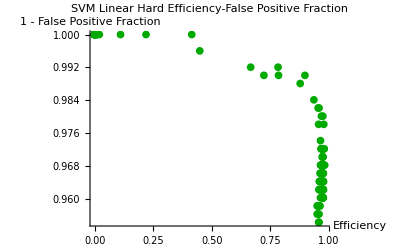

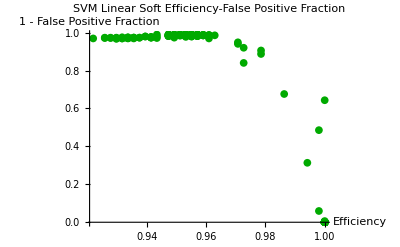

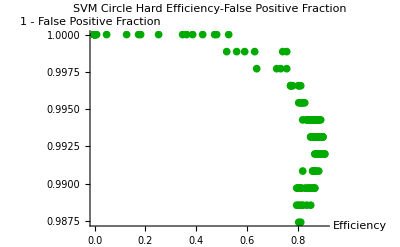

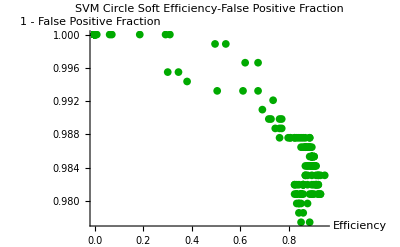

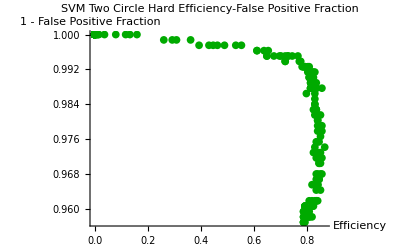

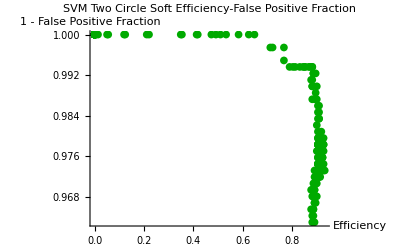

```mathematica
SVMLinearHardEFPPlot
SVMLinearSoftEFPPlot

SVMCircleHardEFPPlot
SVMCircleSoftEFPPlot

SVMTwoCircleHardEFPPlot
SVMTwoCircleSoftEFPPlot
```

#### Efficiency-(1 - False Negative Fraction)

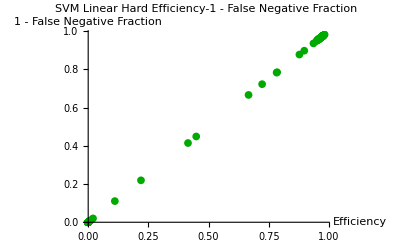

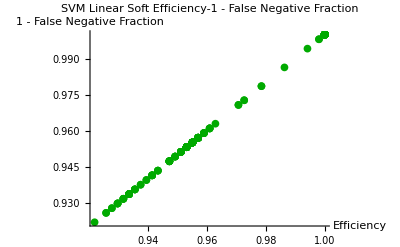

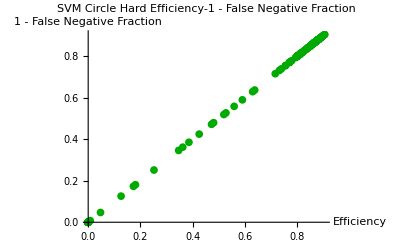

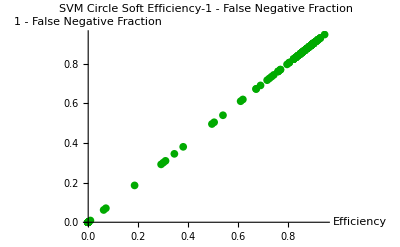

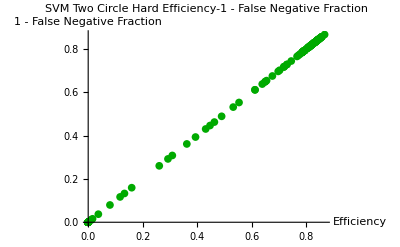

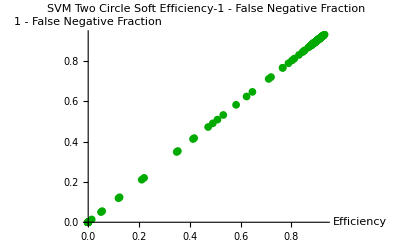

```mathematica
SVMLinearHardEFNPlot
SVMLinearSoftEFNPlot

SVMCircleHardEFNPlot
SVMCircleSoftEFNPlot

SVMTwoCircleHardEFNPlot
SVMTwoCircleSoftEFNPlot
```

#### False Positive Fraction-(1-False Negative Fraction)

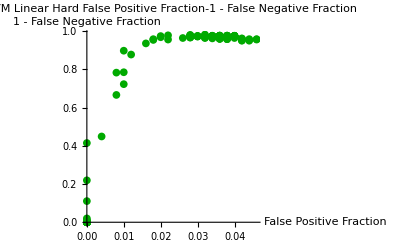

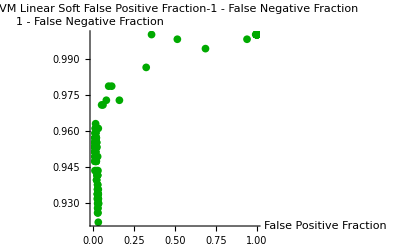

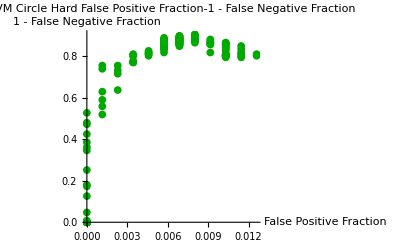

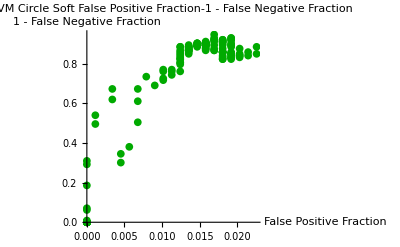

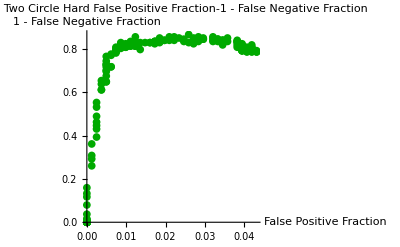

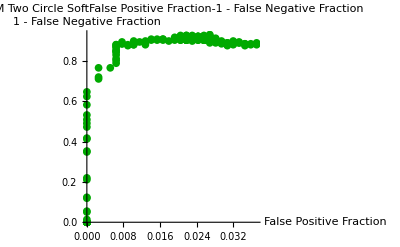

```mathematica
SVMLinearHardFPFNPlot
SVMLinearSoftFPFNPlot

SVMCircleHardFPFNPlot
SVMCircleSoftFPFNPlot

SVMTwoCircleHardFPFNPlot
SVMTwoCircleSoftFPFNPlot
```

### BDT

#### Folds-Stumps-Efficiency

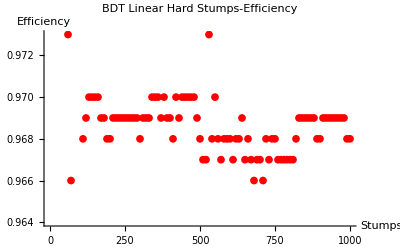

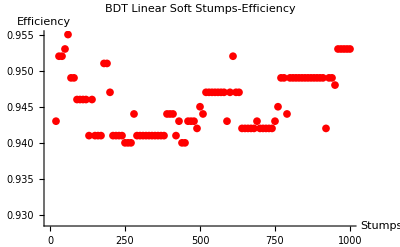

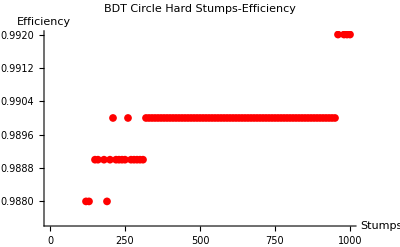

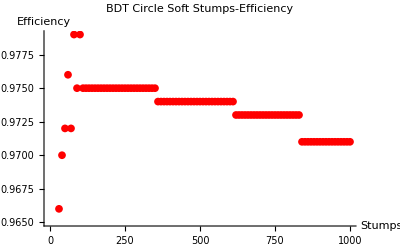

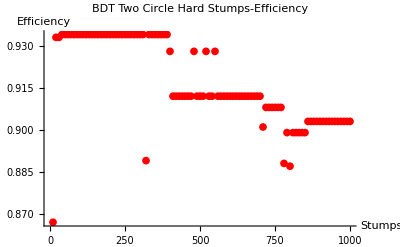

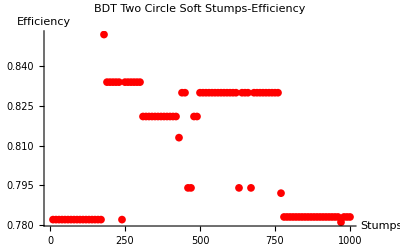

```mathematica
BDTLinearHardSEPlot
BDTLinearSoftSEPlot

BDTCircleHardSEPlot
BDTCircleSoftSEPlot

BDTTwoCircleHardSEPlot
BDTTwoCircleSoftSEPlot
```

#### Efficiency-1 - False Positive Fraction

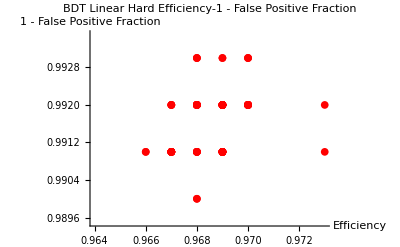

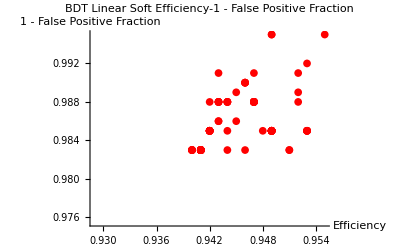

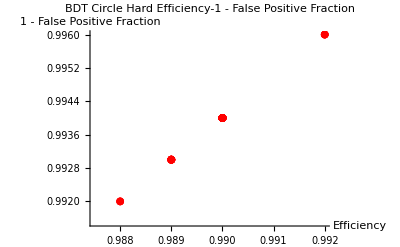

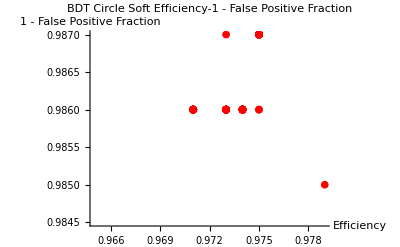

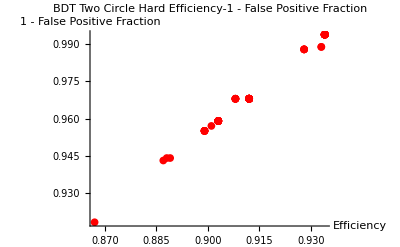

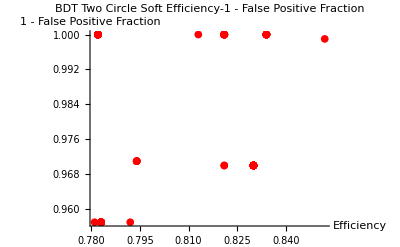

```mathematica
BDTLinearHardEFPPlot
BDTLinearSoftEFPPlot

BDTCircleHardEFPPlot
BDTCircleSoftEFPPlot

BDTTwoCircleHardEFPPlot
BDTTwoCircleSoftEFPPlot
```

#### Efficiency-1 - False Negative Fraction

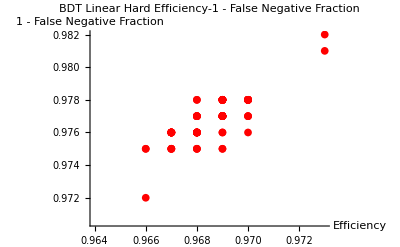

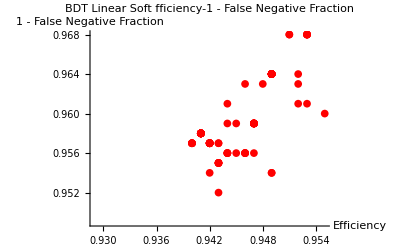

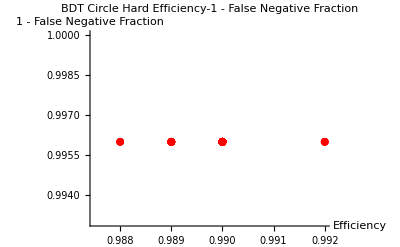

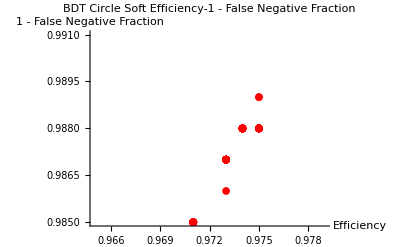

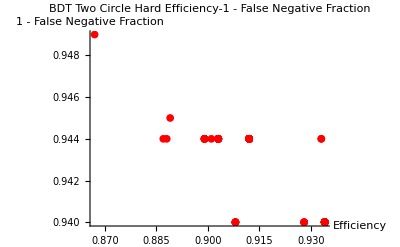

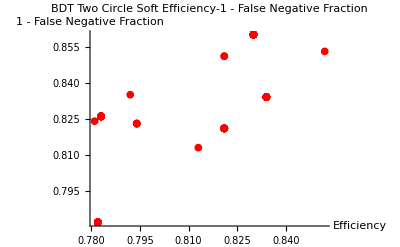

```mathematica
BDTLinearHardEFNPlot
BDTLinearSoftEFNPlot

BDTCircleHardEFNPlot
BDTCircleSoftEFNPlot

BDTTwoCircleHardEFNPlot
BDTTwoCircleSoftEFNPlot
```

#### False Positive Fraction-1 - False Negative Fraction

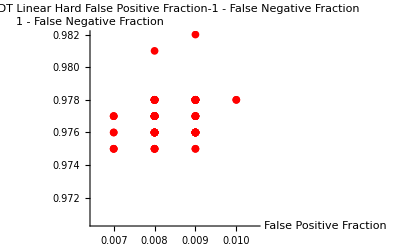

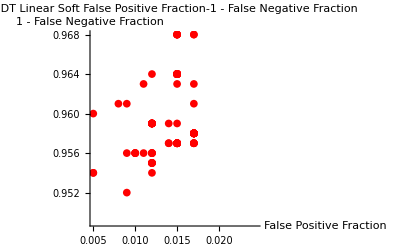

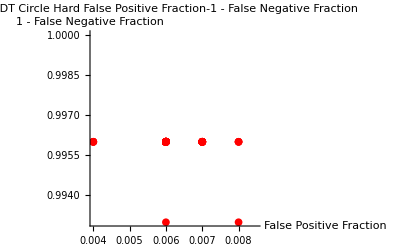

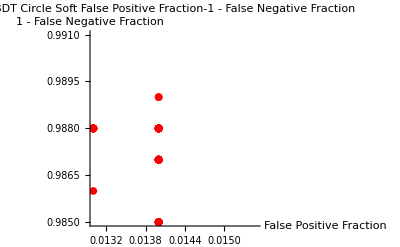

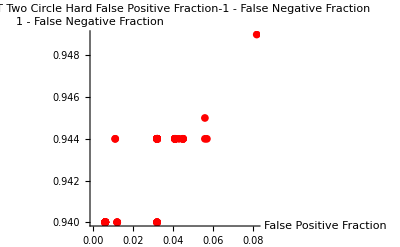

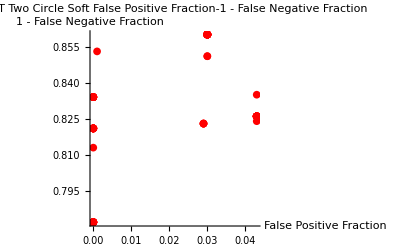

```mathematica
BDTLinearHardFPFNPlot
BDTLinearSoftFPFNPlot

BDTCircleHardFPFNPlot
BDTCircleSoftFPFNPlot

BDTTwoCircleHardFPFNPlot
BDTTwoCircleSoftFPFNPlot
```

### Merged

#### False Positive Fraction- 1 - False Negative Fraction

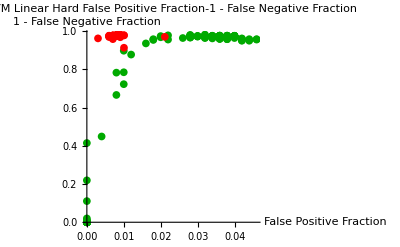

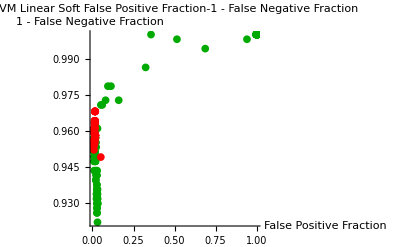

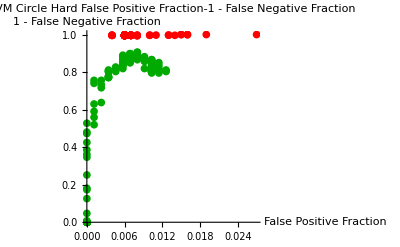

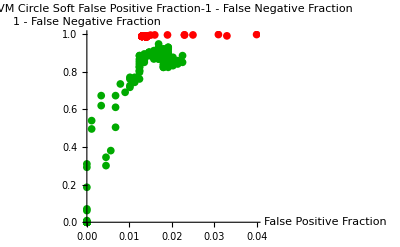

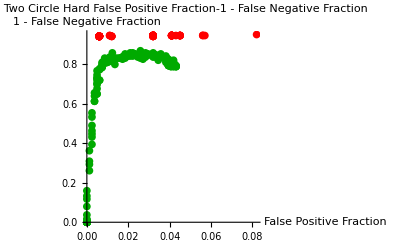

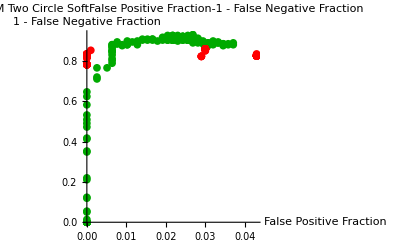

```mathematica
Show[SVMLinearHardFPFNPlot,BDTLinearHardFPFNPlot,PlotRange-> All]
Show[SVMLinearSoftFPFNPlot,BDTLinearSoftFPFNPlot,PlotRange-> All]

Show[SVMCircleHardFPFNPlot,BDTCircleHardFPFNPlot,PlotRange-> All]
Show[SVMCircleSoftFPFNPlot,BDTCircleSoftFPFNPlot,PlotRange-> All]

Show[SVMTwoCircleHardFPFNPlot,BDTTwoCircleHardFPFNPlot,PlotRange-> All]
Show[SVMTwoCircleSoftFPFNPlot,BDTTwoCircleSoftFPFNPlot,PlotRange-> All]
```